## Infinite Square Well Potential

```mathematica
ClearAll["Global`*"]
```

Constants/Parameters

```mathematica
(*Constants (In Atomic Units)*)
me:=1
ℏ:=1
k:=1
ω:=√(me/k)

(*Parameters*)
L:=10
inf:=10^10
numbasis:=12
V0:=10^1
dψ:=0.0001
ϵ:=1
```

Definitions

```mathematica
(*Potential Energy*)
v[x_]:=Piecewise[{{0,-L/2≤x≤L/2}},inf]
visibleV[x_]:=Piecewise[{{0,-L/2≤x≤L/2}},V0]
(*Time Independent Schrodinger Equation*)
H[x_]=(-ℏ^2/(2 me) D[#,{x,2}]+v[x] #)&;
TISE:=ψ''[x]==-(2 me)/ℏ^2 (ϵ-v[x]) ψ[x]
bcs:={ψ[-L/2]==0,ψ'[-L/2]==dψ}
```

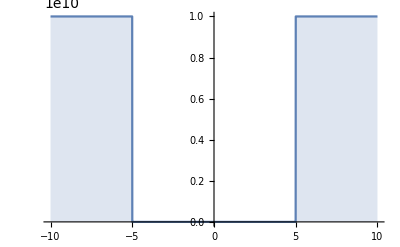

```mathematica
Plot[v[x],{x,-L,L},Exclusions->None,Filling->Axis]
```

```mathematica
basis[n_,x_]:=Sqrt[2/L] Sin[n Pi x/L];
HMatrix:=Table[NIntegrate[basis[m,x] H[x][ basis[n,x]],{x,-L/2,L/2},AccuracyGoal->10],{m,1,numbasis},{n,1,numbasis}]
```

{0.049348,0.197392,0.444132,0.789568,1.2337,1.77653,2.41805,3.15827,3.99719,4.9348,5.97111,7.10612}

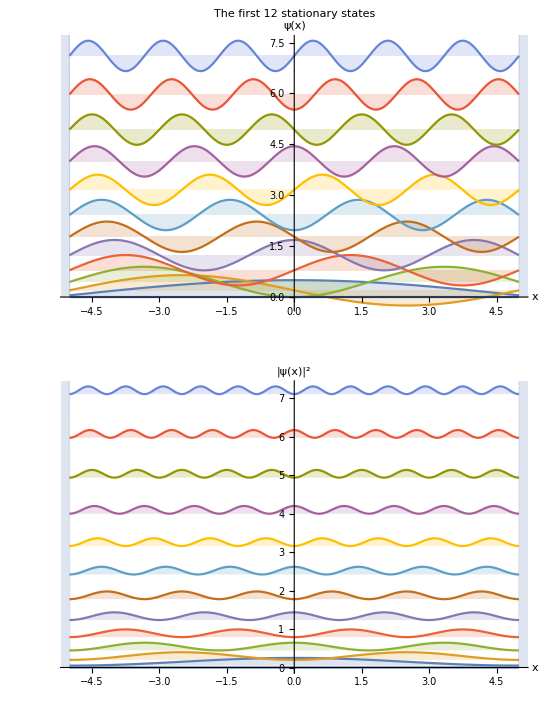

```mathematica
(*True Energy Eigenvalues*)
Sort[Table[1/(2 me) ((n π ℏ)/L)^2//N,{n,1,numbasis}]]
(*Numerical Eigenvalues*)
vals:=Diagonal[HMatrix]

(*Use these Energies to now solve the TISE*)
unnormedfuns:=Table[ψ[x]/.First[Evaluate[NDSolve[{TISE/.ϵ->vals[[i]],bcs},ψ,{x,-L/2,L/2}]]],{i,1,numbasis}]

(*Normalize these functions*)
normfuns:=Map[Sqrt[NIntegrate[Conjugate[#] #,{x,-L/2,L/2}]]&,unnormedfuns]
funs:=unnormedfuns/normfuns

fillingrule:=Table[i->vals[[i]],{i,1,numbasis}]
labels:=Table[ToString[Subscript[ψ, i],TraditionalForm],{i,1,numbasis}]
title:=StringForm["The first `` stationary states",numbasis]

GraphicsColumn[{Show[Plot[Evaluate[funs+vals],{x,-L/2,L/2},AxesLabel->{"x","ψ(x)"},Filling->fillingrule,PlotLabel->title],Plot[visibleV[x],{x,-L,L},Filling->Axis]],Show[Plot[Evaluate[funs^2+vals],{x,-L/2,L/2},AxesLabel->{"x","|ψ(x)|^2"},Filling->fillingrule],Plot[visibleV[x],{x,-L,L},Filling->Axis]]}]
```